0.01==v^2-Cos[theta]

0.5==v^2-Cos[theta]

1==v^2-Cos[theta]

1.1==v^2-Cos[theta]

2==v^2-Cos[theta]

5==v^2-Cos[theta]

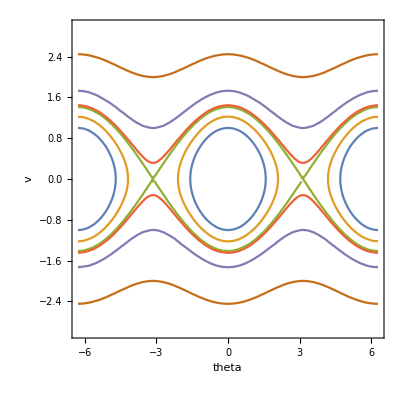

```mathematica
(* Dynamical phase portraits. Note this is to plot the phase portrait of a dynamical system, rather than the phase portrait of a differential equation *)
(* Suppose you are interested in the phase portrait of a pendulum with energy equation E = v^2 - cos(theta). The ``phase portrait'' is a plot of v versus theta for different values of the total energy E *)
E001 = 0.01 == v^2 - Cos[theta]
E05 = 0.5 == v^2 - Cos[theta]
E1 = 1 == v^2 - Cos[theta]
E1p1 = 1.1 == v^2 - Cos[theta]
E2 = 2 == v^2 - Cos[theta]
E5 = 5 == v^2 - Cos[theta]
ContourPlot[{Evaluate[E001],Evaluate[E05],Evaluate[E1],Evaluate[E1p1],Evaluate[E2],Evaluate[E5]}, {theta, -2Pi,2Pi},{v, -3,3}, FrameLabel->{"theta","v"}]
```